## Allee effect

### Solutions for the Allee

```mathematica
m=2;n=1;
allee[y_,r_,α_,β_]:=- y r(1-α y )(1-β y);
Solve[allee[y,r,α,β]==0,y]
```

{{y→0},{y→1/α},{y→1/β}}

### Allee to three player three strategy game

```mathematica
coeffs=CoefficientList[allee[y,r,α,β]/y,y];
B=Table[Subscript[b, i,j,k],{i,1,m},{j,1,m},{k,1,m}];
Table[Subscript[b, m,j,k]=0,{i,1,m},{j,1,m},{k,1,m}];
Subscript[b, 1,2,2]=coeffs⟦1⟧;Subscript[b, 1,1,2]=coeffs⟦2⟧;Subscript[b, 1,2,1]=0;Subscript[b, 1,1,1]=coeffs⟦3⟧;
payoffs=B;
fits[x_]:=Table[∑_(j=1)^m (∑_(k=1)^m (payoffs⟦i,j,k⟧ Subscript[x, j] Subscript[x, k])),{i,1,2}]/.{Subscript[x, 1]->x,Subscript[x, 2]->1-x};
π1[x_]:=fits[x]⟦1⟧;
π2[x_]:=fits[x]⟦2⟧;
πbar[x_]:=x π1[x]+(1-x)π2[x];
dx[x_]:=x(π1[x]-πbar[x]);
Solve[dx[x]==0,x]
```

{-r,r α+r β,-r α β}

{{x→0},{x→1},{x→1/(1+α)},{x→1/(1+β)}}

### Numerical plots

```mathematica
r=1;
α=0.6;β=0.1;
coeffs=CoefficientList[allee[y,r,α,β]/y,y];
Subscript[b, 1,2,2]=coeffs⟦1⟧;Subscript[b, 1,1,2]=coeffs⟦2⟧;Subscript[b, 1,2,1]=0;Subscript[b, 1,1,1]=coeffs⟦3⟧;
payoffs=B;
intfixpt={1/(1+α),1/(1+β)};
```

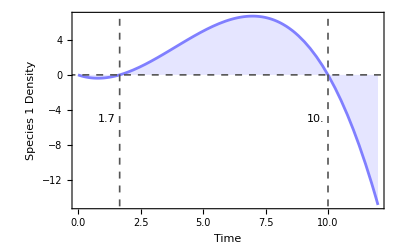

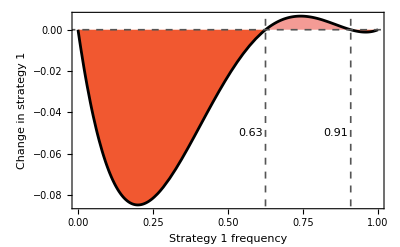

```mathematica
alleeplot=Plot[allee[y,r,α,β],{y,0,12},Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{Style["Time",16,Black],Style["Species 1 Density",16,RGBColor["#807FFF"]]},Epilog->{Inset[SetPrecision[1/α//N,2],{1/α-0.5,-5}],Inset[SetPrecision[1/β//N,2],{1/β-0.5,-5}]},PlotRange->{Automatic,Full},Axes->True,Filling->Axis,GridLines->{{1/α,1/β},{0}},GridLinesStyle->Directive[Darker[Gray],Thickness[0.003], Dashed],PlotStyle->RGBColor["#807FFF"]
]
rp=Plot[dx[x],{x,0,1},PlotRange->{Automatic,Automatic},Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{Style["Strategy 1 frequency",16,RGBColor[0.957,0.606,0.584]],Style["Change in strategy 1",16,RGBColor[0.957,0.606,0.584]]},Filling->Axis,FillingStyle->{RGBColor[0.946,0.346,0.188],RGBColor[0.957,0.606,0.584]},Epilog->{Inset[SetPrecision[intfixpt⟦1⟧,2],{intfixpt⟦1⟧-0.05,-0.05}],Inset[SetPrecision[intfixpt⟦2⟧,2],{intfixpt⟦2⟧-0.05,-0.05}]},GridLines->{intfixpt,{0}},GridLinesStyle->Directive[Darker[Gray],Thickness[0.003], Dashed],PlotStyle->Black]
```